Your Title Here

```mathematica
Manipulate[
Module[{Psat1,Psat2,Tref,CpL1,CpL2,CpV1,CpV2,ΔHvap1,ΔHvap2,nf,Hf1,Hf2,sol,x1,y1,nL,nV,T,amounts,flashcol},
Psat1[t_]:=(1/750.06)*10^(8.08097-1582.271/(t+239.726));(*methanol*)
Psat2[t_]:=(1/750.06)*10^(8.07131-1730.63/(t+233.426));(*water*)

Tref=25;(*°C*)
CpL1=0.11;CpL2=0.076;CpV1=0.052;CpV2=0.034;(*kJ/K/mol*)
ΔHvap1=35.3;ΔHvap2=40.656;(*kJ/mol*)

nf=10;(*moles*)

(*feed*)
Hf1=z1*nf*CpL1*(Tf-Tref);
Hf2=(1-z1)*nf*CpL2*(Tf-Tref);

sol=Quiet@FindRoot[{
Hf1+Hf2==(x*L*CpL1*(t-Tref)+(1-x)*L*CpL2*(t-Tref))+(y*V*(ΔHvap1+CpV1*(t-Tref))+(1-y)*V*(ΔHvap2+CpV2*(t-Tref))),
nf==L+V,
z1*nf==x*L+y*V,
x*Psat1[t]==y*P,
(1-x)*Psat2[t]==(1-y)*P},
{{x,0.5},{y,0.5},{L,5},{V,5},{t,100}}];

x1=x/.sol;y1=y/.sol;nL=L/.sol;nV=V/.sol;T=t/.sol;

amounts[comp_,mol_,title_]:=Module[{val},val=If[#<0,0,#]&/@{comp*mol,(1-comp)*mol};
BarChart[val,ChartStyle->{RGBColor[0.04,0.87,0.26],RGBColor[0,0.4,0.8]},PlotRange->{0,1.2*Max@val},PlotRangePadding->{None,{Scaled@0.1,None}},Frame->False,Axes->False,ImageSize->{120,150},AspectRatio->Full,PlotLabel->Style[Row@{"moles in ",title},17,Black],
Epilog->{
Text[Style[NumberForm[If[#1<0.006,0,#1],{2,1}],17],{#2,#1},{0,-1}]&@@@{{First@val,1},{Last@val,2}},
Text[Style[#1,17],{#2,0},{0,1}]&@@@{{"methanol",1},{"water",2}}
}]
];

flashcol=RGBColor[0.65,0.9,1];
Graphics[{
{flashcol,EdgeForm@flashcol,Disk[{3.5,2.25},{1.5,0.75},{0,π}],Disk[{3.5,-2.25},{1.5,0.75},{π,2*π}],Rectangle[{2,-2.25},{5,2.25}]},
{Thick,Line[{{#,-2.25},{#,2.25}}]&/@{2,5},Circle[{3.5,2.25},{1.5,0.75},{0,π}],Circle[{3.5,-2.25},{1.5,0.75},{π,2*π}]},
{Arrowheads@Large,Arrow[{{0,0},{2,0}}],Arrow[{{3.5,3},{3.5,3.5}, {7, 3.5}}],Arrow[{{3.5,-3},{3.5,-3.5}, {7, -3.5}}]},

Text[Style[Column[{
Row@{NumberForm[T,{3,0}]," °C"},
"flash drum",
Row@{NumberForm[x1*Psat1[T]+(1-x1)*Psat2[T],{4,2}]," bar"}
},Center],17],{3.5,0}],

Text[Style[Row@{NumberForm[Tf,{3,0}]," °C"},17],{-1.9,-2.75}],

Inset[amounts[z1,nf,"feed"],{-1.8,1}],
Inset[amounts[y1,nV,"vapor"],{8.9,4}],
Inset[amounts[x1,nL,"liquid"],{8.9,-2.5}],

Text[Style[Row@{"vapor = ",NumberForm[If[nV<0,0,nV],{2,1}]," mol"},17],{4.5,4.1}],
Text[Style[Row@{"liquid = ",NumberForm[If[nL<0,0,nL],{2,1}]," mol"},17],{4.5,-4.1}],

Text[Style[Row@{"fraction methanol: ",NumberForm[If[y1<0.001,0,y1],{2,2}]},17],{8.8,1}],Text[Style[Row@{"fraction methanol: ",NumberForm[If[x1<0.001,0,x1],{2,2}]},17],{8.8,-5.5}]
},ImageSize->{550,375},PlotRange->{{-4.3,12},{-5.8,6.4}}]
],
Control[{{z1,0.5,"feed mole fraction methanol"},0,1,0.01,Appearance->"Labeled"}],
Control[{{Tf,271,"feed temperature (°C)"},120,300,10,Appearance->"Labeled"}],
Control[{{P,0.25,"flash drum pressure (bar)"},0.25,4,0.25,Appearance->"Labeled"}]
]
```

```mathematica
LightBlue
```

RGBColor[0.87, 0.94, 1]

```mathematica
RGBColor[0.65,0.9,1]
```

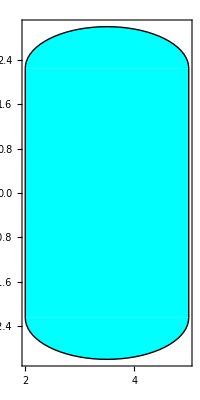

```mathematica
Graphics[{
{Cyan,Disk[{3.5,2.25},{1.5,0.75},{0,π}],Disk[{3.5,-2.25},{1.5,0.75},{π,2*π}],Rectangle[{2,-2.25},{5,2.25}]},
{Thick,Line[{{#,-2.25},{#,2.25}}]&/@{2,5},Circle[{3.5,2.25},{1.5,0.75},{0,π}],Circle[{3.5,-2.25},{1.5,0.75},{π,2*π}]}
},Frame->True]
```

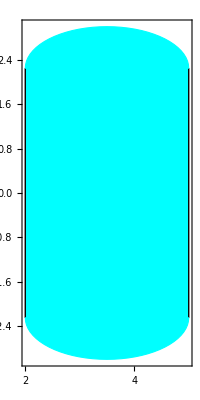

```mathematica
Graphics[{
{Cyan,{EdgeForm@Thick,Disk[{3.5,2.25},{1.5,0.75},{0,π}],Disk[{3.5,-2.25},{1.5,0.75},{π,2*π}]},Rectangle[{2,-2.25},{5,2.25}]},
{Thick,Line[{{#,-2.25},{#,2.25}}]&/@{2,5},Cyan,Line[{{2,#},{5,#}}]&/@{-2.25,2.25}}
},Frame->True]
```

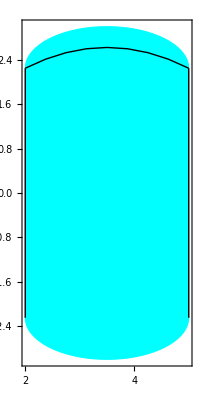

```mathematica
Graphics[{
{EdgeForm@Cyan,Cyan,Disk[{3.5,2.25},{1.5,0.75},{0,π}],Disk[{3.5,-2.25},{1.5,0.75},{π,2*π}],Rectangle[{2,-2.25},{5,2.25}]},
{Thick,Line[{{#,-2.25},{#,2.25}}]&/@{2,5},
BezierCurve[{{2,2.25},{},{3.5,2.25+0.75},{5,2.25}}]
}
},Frame->True]
```

```mathematica
Graphics[{
{EdgeForm@Cyan,Cyan,Disk[{3.5,2.25},{1.5,0.75},{0,π}],Disk[{3.5,-2.25},{1.5,0.75},{π,2*π}],Rectangle[{2,-2.25},{5,2.25}]}
},Frame->True]
```

```mathematica
{EdgeForm@Cyan,Cyan,Disk[{3.5,3},{1.5,0.75},{0,π}],Disk[{3.5,-3},{1.5,0.75},{π,2*π}],Rectangle[{2,-3},{5,3}]}
```

```mathematica
(*Text[Style[Row@{NumberForm[Tf,{3,0}]," °C"},17],{-1.9,-2.75}],

Inset[amounts[z1,nf,"feed"],{-1.8,1}],
Inset[amounts[y1,nV,"vapor"],{8.9,4}],
Inset[amounts[x1,nL,"liquid"],{8.9,-2.5}],

Text[Style[Row@{"vapor = ",NumberForm[If[nV<0,0,nV],{2,1}]," mol"},17],{4.5,4.1}],
Text[Style[Row@{"liquid = ",NumberForm[If[nL<0,0,nL],{2,1}]," mol"},17],{4.5,-4.1}],

Text[Style[Row@{"fraction methanol: ",NumberForm[If[y1<0.001,0,y1],{2,2}]},17],{8.8,1}],Text[Style[Row@{"fraction methanol: ",NumberForm[If[x1<0.001,0,x1],{2,2}]},17],{8.8,-5.5}]*)
```





```mathematica
Control[{{z1,0.33,"feed mole fraction methanol"},0,1,0.01,Appearance->"Labeled"}],
Control[{{Tf,120,"feed temperature (°C)"},120,300,10,Appearance->"Labeled"}],
Control[{{P,4,"flash drum pressure (bar)"},0.25,4,0.25,Appearance->"Labeled"}]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX